## Kinematics

```mathematica
SetDirectory[NotebookDirectory[]]
Get["EVA_luminosity.m"];
Clear[pwz,pwph,pt]
MetricM={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
```

/Users/jasy/Desktop/Research/VLQ/drive-download-20230222T013835Z-001/ZP/Plot Partonic

Get::noopen: Cannot open EVA_luminosity.m.

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
pwz=Sqrt[E0^2-mZ^2];
pwph=Sqrt[E0^2];
pt=Sqrt[E0^2-mt^2];
p10={E0,0,0,pwph};
p20={E0,0,0,-pwz};
k10={E0,pt Sin[θ],0,pt Cos[θ]};
k20={E0,-pt Sin[θ],0,-pt Cos[θ]};
ep10=1/Sqrt[2]{0,-1,-I,0};ep20={pwz/mZ,0,0,-E0/mZ};
```

```mathematica
SPro[a_,b_]:=a.MetricM.b
```

## Spinor Definition from Reece

```mathematica
uplus[e_, p_, θ_] := {Sqrt[e - p] Cos[θ/2], Sqrt[e-p] Sin[θ/2], Sqrt[e+p] Cos[θ/2], Sqrt[e+p]  Sin[θ/2]};
```

```mathematica
uminus[e_, p_, θ_] := {-Sqrt[e + p ]Sin[θ/2], Sqrt[e+p]Cos[θ/2], -Sqrt[e-p]  Sin[θ/2], Sqrt[e-p] Cos[θ/2]};
```

```mathematica
vplus[e_, p_, θ_] := {-Sqrt[e + p] Sin[θ/2], Sqrt[e+p]Cos[θ/2], Sqrt[e-p]  Sin[θ/2], -Sqrt[e-p] Cos[θ/2]};
```

```mathematica
vminus[e_, p_, θ_] := {-Sqrt[e - p] Cos[θ/2], -Sqrt[e-p]  Sin[θ/2], Sqrt[e+p] Cos[θ/2], Sqrt[e+p]  Sin[θ/2]};
```

```mathematica
IdM={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
γ0 = {{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
```

```mathematica
γ1 = {{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
```

```mathematica
γ2 = {{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
```

```mathematica
γ3 = {{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
```

```mathematica
γ5 = {{-1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
PL=(IdM-γ5)/2;
PR=(γ5 +IdM)/2;
```

```mathematica
uplusbar[e_, p_, θ_] := {Sqrt[e - p] Cos[θ/2], Sqrt[e-p] Sin[θ/2], Sqrt[e+p] Cos[θ/2], Sqrt[e+p] Sin[θ/2]}.γ0;
```

```mathematica
uminusbar[e_, p_, θ_] := {-Sqrt[e + p] Sin[θ/2], Sqrt[e+p]Cos[θ/2], -Sqrt[e-p]  Sin[θ/2], Sqrt[e-p] Cos[θ/2]}.γ0;
```

```mathematica
vplusbar[e_, p_, θ_] := {-Sqrt[e + p] Sin[θ/2], Sqrt[e+p]Cos[θ/2], Sqrt[e-p]  Sin[θ/2], -Sqrt[e-p] Cos[θ/2]}.γ0;
```

```mathematica
vminusbar[e_, p_, θ_] := {-Sqrt[e - p] Cos[θ/2], -Sqrt[e-p] Sin[θ/2], Sqrt[e+p] Cos[θ/2], Sqrt[e+p] Sin[θ/2]}.γ0;
```

```mathematica
uminusbar[E0,pt,θ].vminus[E0,pt,-θ]//Simplify
uminusbar[E0,pt,θ].vplus[E0,pt,-θ]//Simplify
uplusbar[E0,pt,θ].vplus[E0,pt,-θ]//Simplify
uplusbar[E0,pt,θ].vminus[E0,pt,-θ]//Simplify
```

-2 √(E0^2-mt^2) Sin[θ]

0

2 √(E0^2-mt^2) Sin[θ]

0

## Amplitude

### Diagram 1

```mathematica
Amp1[ubar_,v_]:=(1/3) 1/(SPro[k20-p20,k20-p20]-mt^2) 2 I ee (ubar . GaMatrixPro[ep10]. (mt IdM- GaMatrixPro[k20 -p20 ]).(I ee GaMatrixPro[ep20]. ((((1/2-(2 sint^2)/3)(1 - dyt))/(cost sint) PL) -((2sint)/(3 cost) PR))).v);
```

### Diagram 2

```mathematica
GaMatrixPro[p_]:=p[[1]]γ0-p[[2]]γ1-p[[3]]γ2-p[[4]]γ3
```

```mathematica
Amp2[ubar_,v_]:=(1/3) 1/(SPro[p20-k10,p20-k10]-mt^2) 2  I  ee (ubar . GaMatrixPro[ep20].(-I ee  ((((-1/2+(2 sint^2)/3)(1 - dyt))/(cost  sint) PL) +((2sint)/(3 cost)  PR))). (mt IdM + GaMatrixPro[k10 -p20 ]).GaMatrixPro[ep10].v);//Simplify;
```

### Diagram 3

```mathematica
Amp3[ubar_,v_]:=(1/3) 1/(SPro[k20-p20,k20-p20]-mt^2) 2 I ee (ubar . GaMatrixPro[ep10]. (mt IdM- GaMatrixPro[k20 -p20 ]).(I ee GaMatrixPro[ep20]. ((((-(2 sint^2)/3)(dyt))/(cost sint) PL) )).v);
```

### Diagram 4

```mathematica
GaMatrixPro[p_]:=p[[1]]γ0-p[[2]]γ1-p[[3]]γ2-p[[4]]γ3
```

```mathematica
Amp4[ubar_,v_]:=(1/3) 1/(SPro[p20-k10,p20-k10]-mt^2) 2  I  ee (ubar . GaMatrixPro[ep20].(-I ee  (((((2 sint^2)/3)(dyt))/(cost  sint) PL) )). (mt IdM + GaMatrixPro[k10 -p20 ]).GaMatrixPro[ep10].v);//Simplify;
```

## Total Amplitude

```mathematica
AmpTotal[ubar_,v_]:=Amp1[ubar,v]+Amp2[ubar,v] + Amp3[ubar,v]+Amp4[ubar,v];
```

```mathematica
app=AmpTotal[uplusbar[E0,pt,θ],vplus[E0,pt,Pi+θ]]//TrigReduce//Simplify;
apm=AmpTotal[uplusbar[E0,pt,θ],vminus[E0,pt,Pi+θ]]//TrigReduce//Simplify;
amp=AmpTotal[uminusbar[E0,pt,θ],vplus[E0,pt,Pi+θ]]//TrigReduce//Simplify;
amm=AmpTotal[uminusbar[E0,pt,θ],vminus[E0,pt,Pi+θ]]//TrigReduce//Simplify;
```

## Parameter choice

```mathematica
Nc=3;
```

```mathematica
para={mW->80.379,mZ->91.1876,mh->125.,mt->173,sint->0.479,cost->0.878,ee->0.3128};
Msquare=Nc(app^2+apm^2+amp^2+amm^2);
```

## Integrated over the phase space

```mathematica
dsigma=(1/(4 E0^2( 1+(pwz/E0)))pt/((2Pi)^2 4*2E0)Msquare)//.para;
dsigma0=dsigma//.dyt->0;
dsigmasL=dsigma//.dyt->0.01;
```

```mathematica
factorpb = 0.3894 * 10^9;
fyu [dytt_] := NIntegrate[(dsigma //. {E0 -> 3000, dyt -> dytt} //Simplify) Sin[θ] 2 Pi , { θ , 0 , Pi}]
fyu[0.00] * factorpb
```

0.396293

```mathematica
sqrtsList=Table[350+25*i,{i,0,400}];
thetaList=Table[0+(Pi/18)*i,{i,0,18}];
```

```mathematica
sigSM=Table[NIntegrate[2Pi Sin[θ](dsigma0//.{E0->sqrtsList[[i]]/2}),{θ,0,Pi}],{i,1,Length@sqrtsList}];
sigSL=Table[NIntegrate[2Pi Sin[θ](dsigmasL//.{E0->sqrtsList[[i]]/2}),{θ,0,Pi}],{i,1,Length@sqrtsList}];
```

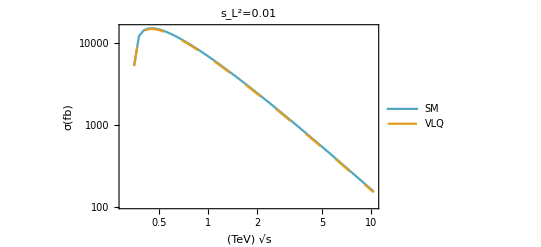

```mathematica
factor=0.3894*10^12;
lineplot=ListLogLogPlot[{Transpose[{sqrtsList/10^3,factor*sigSM}],Transpose[{sqrtsList/10^3,factor*sigSL}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],Dashing[Large]},Frame->True,FrameLabel->{Style[DisplayForm[SqrtBox["s"]]"(TeV)",Black,20,FontFamily->"Times"],Style["σ(fb)",Black,20,FontFamily->"Times"]},
PlotLabel->Style["s_L^2=0.01",Black,20],
PlotLegends->Placed[{Style["SM",Black,10,FontFamily->"Times"],Style["VLQ",Black,10,FontFamily->"Times"]},{0.8,0.8}],
FrameTicksStyle->Directive[Black,13]]
```